# GetCircuitSuperoperator

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
CreateLocalQuESTEnv["../quest_link"];
```

## Doc

```mathematica
?GetCircuitSuperoperator
```

```mathematica
?AssertValidChannels
```

## Correctness

```mathematica
(* this method can only test when AssertValidChannels -> True (default),
   and when all gate parameters are given numeric values *)
test[circ_, subs_:{}] := Module[
	{n, in, out, sup, ρ, err},
	n = 1 + Max @ GetCircuitQubits @ circ;
	in = RandomComplex[{-1-ⅈ,1+ⅈ}, {2^n,2^n}];
	ρ = SetQuregMatrix[CreateDensityQureg[n], in];
	ApplyCircuit[ρ, circ /. subs];
	sup = GetCircuitSuperoperator[circ];
	out = CalcCircuitMatrix[sup /. subs, 2 n] . Flatten @ Transpose @ in;
	err = Flatten @ Transpose @ GetQuregState[ρ] - out // N // Abs // Max // Chop;
	Echo[sup, "output: "];
	Echo[err, "error: "];
	If[err =!= 0 && err =!= 0., Style["ERRONEOUS SUPEROPERATOR!", Red]]]
```

## Gates

### Uncontrolled

```mathematica
test @ Subscript[H, 2]
```

output:   {H_2,H_5}

error:   0

```mathematica
test @ Subscript[Id, 2]
```

output:   {Id_2,Id_5}

error:   0

```mathematica
test @ Subscript[S, 2]
```

output:   {S_2,Ph_5[-π/2]}

error:   0

```mathematica
test @ Subscript[T, 1]
```

output:   {T_1,Ph_3[-π/4]}

error:   0

```mathematica
test @ Subscript[SWAP, 0,1]
```

output:   {SWAP_(0,1),SWAP_(2,3)}

error:   0

```mathematica
test @ Subscript[X, 0]
test @ Subscript[Y, 1]
test @ Subscript[Z, 2]
```

output:   {X_0,X_1}

error:   0

output:   {Y_1,U_3[{{0,ⅈ},{-ⅈ,0}}]}

error:   0

output:   {Z_2,Z_5}

error:   0

```mathematica
test[Subscript[Ph, 1,3,0][x], x->RandomReal[]]
```

output:   {Ph_(1,3,0)[x],Ph_(5,7,4)[-x]}

error:   0

```mathematica
test[R[x, Subscript[X, 0] Subscript[X, 1] Subscript[Z, 2]], x->RandomReal[]]
test[R[x, Subscript[Y, 0] Subscript[Y, 1] Subscript[Z, 2]], x->RandomReal[]]
test[R[x, Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2]], x->RandomReal[]]
```

output:   {R[x,X_0 X_1 Z_2],R[-x,X_3 X_4 Z_5]}

error:   0

output:   {R[x,Y_0 Y_1 Z_2],R[-x,Y_3 Y_4 Z_5]}

error:   0

output:   {R[x,X_0 Y_1 Z_2],R[x,X_3 Y_4 Z_5]}

error:   0

```mathematica
test[Subscript[Rx, 0][x], x->RandomReal[]]
test[Subscript[Rx, 0,2,3][x], x->RandomReal[]]
test[Subscript[Ry, 0][x], x->RandomReal[]]
test[Subscript[Ry, 0,2,3][x], x->RandomReal[]]
test[Subscript[Rz, 0][x], x->RandomReal[]]
test[Subscript[Rz, 0,2,3][x], x->RandomReal[]]
```

output:   {Rx_0[x],Rx_1[-x]}

error:   0

output:   {Rx_(0,2,3)[x],Rx_(4,6,7)[-x]}

error:   0

output:   {Ry_0[x],Ry_1[x]}

error:   0

output:   {Ry_(0,2,3)[x],Ry_(4,6,7)[x]}

error:   0

output:   {Rz_0[x],Rz_1[-x]}

error:   0

output:   {Rz_(0,2,3)[x],Rz_(4,6,7)[-x]}

error:   0

```mathematica
test @ Subscript[U, 0,1]@ RandomVariate @ CircularUnitaryMatrixDistribution @ 4
```

output:   {U_(0,1)[{{0.181902+0.219331 ⅈ,-0.508232+0.0095965 ⅈ,0.205379+0.633037 ⅈ,-0.427538-0.186302 ⅈ},{-0.345852-0.565724 ⅈ,-0.684023-0.0271223 ⅈ,-0.0370904-0.28199 ⅈ,-0.0153565-0.10291 ⅈ},{0.187056+0.504434 ⅈ,-0.433917-0.20901 ⅈ,-0.233328-0.340244 ⅈ,-0.00833779+0.555257 ⅈ},{-0.287874-0.326854 ⅈ,0.107756-0.171478 ⅈ,-0.143546+0.534206 ⅈ,0.00331872+0.680651 ⅈ}}],U_(2,3)[{{0.181902-0.219331 ⅈ,-0.508232-0.0095965 ⅈ,0.205379-0.633037 ⅈ,-0.427538+0.186302 ⅈ},{-0.345852+0.565724 ⅈ,-0.684023+0.0271223 ⅈ,-0.0370904+0.28199 ⅈ,-0.0153565+0.10291 ⅈ},{0.187056-0.504434 ⅈ,-0.433917+0.20901 ⅈ,-0.233328+0.340244 ⅈ,-0.00833779-0.555257 ⅈ},{-0.287874+0.326854 ⅈ,0.107756+0.171478 ⅈ,-0.143546-0.534206 ⅈ,0.00331872-0.680651 ⅈ}}]}

error:   0

```mathematica
test @ Subscript[UNonNorm, 0,1]@ RandomComplex[{-1-ⅈ,1+ⅈ},{4,4}]
```

output:   {UNonNorm_(0,1)[{{-0.511282+0.248489 ⅈ,-0.633082-0.195985 ⅈ,-0.121728+0.180578 ⅈ,0.976429+0.549827 ⅈ},{-0.138027-0.106615 ⅈ,0.128053-0.336605 ⅈ,-0.0617404-0.856429 ⅈ,-0.13735-0.111372 ⅈ},{0.203453-0.173808 ⅈ,0.944329+0.29189 ⅈ,-0.906104-0.308604 ⅈ,0.739776-0.960591 ⅈ},{-0.641016+0.752223 ⅈ,0.131106-0.156225 ⅈ,-0.0873335-0.997022 ⅈ,0.91434-0.810842 ⅈ}}],UNonNorm_(2,3)[{{-0.511282-0.248489 ⅈ,-0.633082+0.195985 ⅈ,-0.121728-0.180578 ⅈ,0.976429-0.549827 ⅈ},{-0.138027+0.106615 ⅈ,0.128053+0.336605 ⅈ,-0.0617404+0.856429 ⅈ,-0.13735+0.111372 ⅈ},{0.203453+0.173808 ⅈ,0.944329-0.29189 ⅈ,-0.906104+0.308604 ⅈ,0.739776+0.960591 ⅈ},{-0.641016-0.752223 ⅈ,0.131106+0.156225 ⅈ,-0.0873335+0.997022 ⅈ,0.91434+0.810842 ⅈ}}]}

error:   0

### Controlled

```mathematica
GetCircuitSuperoperator @ Subscript[C, 1]@Subscript[H, 2]
```

{C_1[H_2],C_4[H_5]}

```mathematica
test @ Subscript[C, 0]@ Subscript[Id, 2]
```

output:   {C_0[Id_2],C_3[Id_5]}

error:   0

```mathematica
test @ Subscript[C, 1]@Subscript[S, 2]
```

output:   {C_1[S_2],C_4[Ph_5[-π/2]]}

error:   0

```mathematica
test @ Subscript[C, 0,2]@Subscript[T, 1]
```

output:   {C_(0,2)[T_1],C_(3,5)[Ph_4[-π/4]]}

error:   0

```mathematica
test @ Subscript[C, 2,3]@Subscript[SWAP, 0,1]
```

output:   {C_(2,3)[SWAP_(0,1)],C_(6,7)[SWAP_(4,5)]}

error:   0

```mathematica
test @ Subscript[C, 1,2,3] @ Subscript[X, 0]
test @ Subscript[C, 2]@Subscript[Y, 1]
test @ Subscript[C, 3]@Subscript[Z, 2]
```

output:   {C_(1,2,3)[X_0],C_(5,6,7)[X_4]}

error:   0

output:   {C_2[Y_1],C_5[U_4[{{0,ⅈ},{-ⅈ,0}}]]}

error:   0

output:   {C_3[Z_2],C_7[Z_6]}

error:   0

```mathematica
test[Subscript[C, 2,4]@Subscript[Ph, 1,3,0][x], x->RandomReal[]]
```

output:   {C_(2,4)[Ph_(1,3,0)[x]],C_(7,9)[Ph_(6,8,5)[-x]]}

error:   0

```mathematica
test[Subscript[C, 3]@R[x, Subscript[X, 0] Subscript[X, 1] Subscript[Z, 2]], x->RandomReal[]]
test[Subscript[C, 3,4]@R[x, Subscript[Y, 0] Subscript[Y, 1] Subscript[Z, 2]], x->RandomReal[]]
test[Subscript[C, 3]@R[x, Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2]], x->RandomReal[]]
```

output:   {C_3[R[x,X_0 X_1 Z_2]],C_7[R[-x,X_4 X_5 Z_6]]}

error:   0

output:   {C_(3,4)[R[x,Y_0 Y_1 Z_2]],C_(8,9)[R[-x,Y_5 Y_6 Z_7]]}

error:   0

output:   {C_3[R[x,X_0 Y_1 Z_2]],C_7[R[x,X_4 Y_5 Z_6]]}

error:   0

```mathematica
test[Subscript[C, 1,2]@ Subscript[Rx, 0][x], x->RandomReal[]]
test[Subscript[C, 1]@Subscript[Rx, 0,2,3][x], x->RandomReal[]]
test[Subscript[C, 1,2,3]@ Subscript[Ry, 0][x], x->RandomReal[]]
test[Subscript[C, 1]@ Subscript[Ry, 0,2,3][x], x->RandomReal[]]
test[Subscript[C, 1,2,3]@Subscript[Rz, 0][x], x->RandomReal[]]
test[Subscript[C, 1,4]@Subscript[Rz, 0,2,3][x], x->RandomReal[]]
```

output:   {C_(1,2)[Rx_0[x]],C_(4,5)[Rx_3[-x]]}

error:   0

output:   {C_1[Rx_(0,2,3)[x]],C_5[Rx_(4,6,7)[-x]]}

error:   0

output:   {C_(1,2,3)[Ry_0[x]],C_(5,6,7)[Ry_4[x]]}

error:   0

output:   {C_1[Ry_(0,2,3)[x]],C_5[Ry_(4,6,7)[x]]}

error:   0

output:   {C_(1,2,3)[Rz_0[x]],C_(5,6,7)[Rz_4[-x]]}

error:   0

output:   {C_(1,4)[Rz_(0,2,3)[x]],C_(6,9)[Rz_(5,7,8)[-x]]}

error:   0

```mathematica
test @ Subscript[C, 2,3]@ Subscript[U, 0,1]@ RandomVariate @ CircularUnitaryMatrixDistribution @ 4
```

output:   {C_(2,3)[U_(0,1)[{{-0.0506663+0.299448 ⅈ,-0.178197+0.789933 ⅈ,0.29792+0.0345961 ⅈ,0.216312+0.339517 ⅈ},{-0.37405+0.226039 ⅈ,0.301695-0.150532 ⅈ,-0.517628-0.0356516 ⅈ,0.105163+0.644239 ⅈ},{0.00784152-0.482321 ⅈ,0.300719+0.300631 ⅈ,-0.167931+0.73856 ⅈ,-0.109945+0.0270907 ⅈ},{0.637247-0.279245 ⅈ,-0.0280165-0.221306 ⅈ,0.253307-0.0547739 ⅈ,-0.0105128+0.631587 ⅈ}}]],C_(6,7)[U_(4,5)[{{-0.0506663-0.299448 ⅈ,-0.178197-0.789933 ⅈ,0.29792-0.0345961 ⅈ,0.216312-0.339517 ⅈ},{-0.37405-0.226039 ⅈ,0.301695+0.150532 ⅈ,-0.517628+0.0356516 ⅈ,0.105163-0.644239 ⅈ},{0.00784152+0.482321 ⅈ,0.300719-0.300631 ⅈ,-0.167931-0.73856 ⅈ,-0.109945-0.0270907 ⅈ},{0.637247+0.279245 ⅈ,-0.0280165+0.221306 ⅈ,0.253307+0.0547739 ⅈ,-0.0105128-0.631587 ⅈ}}]]}

error:   0

```mathematica
test @ Subscript[C, 2,3]@Subscript[UNonNorm, 0,1]@ RandomComplex[{-1-ⅈ,1+ⅈ},{4,4}]
```

output:   {C_(2,3)[UNonNorm_(0,1)[{{0.0508448+0.720073 ⅈ,-0.585396+0.256124 ⅈ,0.725307-0.446057 ⅈ,-0.384357-0.363043 ⅈ},{0.10545+0.582045 ⅈ,0.16316-0.343721 ⅈ,0.424913+0.637291 ⅈ,0.765014-0.709477 ⅈ},{0.50184+0.700342 ⅈ,0.975469-0.318192 ⅈ,-0.932429-0.834725 ⅈ,0.662282-0.238005 ⅈ},{-0.366955-0.95043 ⅈ,0.112315+0.844756 ⅈ,0.0760064+0.00691771 ⅈ,-0.0920667+0.29749 ⅈ}}]],C_(6,7)[UNonNorm_(4,5)[{{0.0508448-0.720073 ⅈ,-0.585396-0.256124 ⅈ,0.725307+0.446057 ⅈ,-0.384357+0.363043 ⅈ},{0.10545-0.582045 ⅈ,0.16316+0.343721 ⅈ,0.424913-0.637291 ⅈ,0.765014+0.709477 ⅈ},{0.50184-0.700342 ⅈ,0.975469+0.318192 ⅈ,-0.932429+0.834725 ⅈ,0.662282+0.238005 ⅈ},{-0.366955+0.95043 ⅈ,0.112315-0.844756 ⅈ,0.0760064-0.00691771 ⅈ,-0.0920667-0.29749 ⅈ}}]]}

error:   0

### Special

```mathematica
test[{G[x], Subscript[Id, 0]}, x->RandomReal[]]
```

output:   {Id_0,Id_1}

error:   0

```mathematica
test[{Fac[x], Subscript[Id, 0]}, x->RandomReal[]]
```

output:   {Fac[x],Id_0,Id_1}

error:   0

```mathematica
test[Subscript[Matr, 0][{{1,2},{3,4}}]]
```

output:   {Matr_0[{{1,2},{3,4}}]}

error:   0

## Channels

```mathematica
test[Subscript[Damp, 0][x], x->.2]
```

output:   {Matr_(0,1)[{{1,0,0,x},{0,√(1-x),0,0},{0,0,√(1-x),0},{0,0,0,1-x}}]}

error:   0

```mathematica
test[Subscript[Deph, 0][x], x->.1]
test[Subscript[Deph, 1,2][x], x->.4]
```

output:   {Matr_(0,1)[{{1,0,0,0},{0,1-2 x,0,0},{0,0,1-2 x,0},{0,0,0,1}}]}

error:   0

output:   {Matr_(1,2,4,5)[{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1-(4 x)/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1-(4 x)/3,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1-(4 x)/3,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1-(4 x)/3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1-(4 x)/3,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1-(4 x)/3,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1-(4 x)/3,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1-(4 x)/3,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1-(4 x)/3,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1-(4 x)/3,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1-(4 x)/3,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1-(4 x)/3,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}]}

error:   0

```mathematica
test[Subscript[Depol, 0][x], x->.1]
test[Subscript[Depol, 1,2][x], x->.4]
```

output:   {Matr_(0,1)[{{1-(2 x)/3,0,0,(2 x)/3},{0,1-(4 x)/3,0,0},{0,0,1-(4 x)/3,0},{(2 x)/3,0,0,1-(2 x)/3}}]}

error:   0

output:   {Matr_(1,2,4,5)[{{1-(4 x)/5,0,0,0,0,(4 x)/15,0,0,0,0,(4 x)/15,0,0,0,0,(4 x)/15},{0,1-(16 x)/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1-(16 x)/15,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1-(16 x)/15,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1-(16 x)/15,0,0,0,0,0,0,0,0,0,0,0},{(4 x)/15,0,0,0,0,1-(4 x)/5,0,0,0,0,(4 x)/15,0,0,0,0,(4 x)/15},{0,0,0,0,0,0,1-(16 x)/15,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1-(16 x)/15,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1-(16 x)/15,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1-(16 x)/15,0,0,0,0,0,0},{(4 x)/15,0,0,0,0,(4 x)/15,0,0,0,0,1-(4 x)/5,0,0,0,0,(4 x)/15},{0,0,0,0,0,0,0,0,0,0,0,1-(16 x)/15,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1-(16 x)/15,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1-(16 x)/15,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1-(16 x)/15,0},{(4 x)/15,0,0,0,0,(4 x)/15,0,0,0,0,(4 x)/15,0,0,0,0,1-(4 x)/5}}]}

error:   0

```mathematica
m = Table[RandomVariate @ CircularUnitaryMatrixDistribution @ 4,1];
test[Subscript[Kraus, 0,1][m]]
```

output:   {Matr_(0,1,2,3)[{{0.276075+0. ⅈ,-0.107384+0.378888 ⅈ,-0.0833896-0.16882 ⅈ,-0.0666051+0.0698553 ⅈ,-0.107384-0.378888 ⅈ,0.561759+0. ⅈ,-0.199255+0.18011 ⅈ,0.121777+0.0642383 ⅈ,-0.0833896+0.16882 ⅈ,-0.199255-0.18011 ⅈ,0.128422+0. ⅈ,-0.0225982-0.0618291 ⅈ,-0.0666051-0.0698553 ⅈ,0.121777-0.0642383 ⅈ,-0.0225982+0.0618291 ⅈ,0.0337444+0. ⅈ},{0.113455+0.148148 ⅈ,0.0882889+0.173687 ⅈ,0.240396+0.2404 ⅈ,0.263158-0.135861 ⅈ,0.15919-0.213331 ⅈ,0.204029-0.188727 ⅈ,0.236422-0.42343 ⅈ,-0.288816-0.308316 ⅈ,-0.124862+0.0246289 ⅈ,-0.132878+0.00152585 ⅈ,-0.219618+0.0743885 ⅈ,0.00359082+0.201959 ⅈ,0.0101141-0.0644492 ⅈ,0.0226477-0.064243 ⅈ,0.00283116-0.118826 ⅈ,-0.0978657-0.0338095 ⅈ},{0.0603701+0.0770828 ⅈ,0.0851857+0.0347236 ⅈ,0.0875352+0.275605 ⅈ,-0.408949+0.0846542 ⅈ,0.0823074-0.112835 ⅈ,0.0145208-0.130416 ⅈ,0.344195-0.227335 ⅈ,0.275248+0.528319 ⅈ,-0.0653712+0.0136332 ⅈ,-0.0469642+0.0416027 ⅈ,-0.194973-0.0297198 ⅈ,0.0717587-0.275643 ⅈ,0.00493953-0.0338722 ⅈ,-0.0117655-0.0299318 ⅈ,0.0486178-0.0886407 ⅈ,0.120082+0.083053 ⅈ},{0.352123-0.177372 ⅈ,-0.153346-0.225938 ⅈ,-0.0989889+0.177817 ⅈ,0.0590234-0.0340435 ⅈ,-0.380391-0.414266 ⅈ,-0.250434+0.298335 ⅈ,0.282542+0.0666885 ⅈ,-0.0696797-0.0677626 ⅈ,0.00210264+0.268899 ⅈ,0.18448-0.0255253 ⅈ,-0.0788354-0.114242 ⅈ,0.00298936+0.0463758 ⅈ,-0.129833-0.0463055 ⅈ,-0.0201734+0.0933103 ⅈ,0.0688749-0.0178526 ⅈ,-0.0228538-0.00672144 ⅈ},{0.113455-0.148148 ⅈ,0.15919+0.213331 ⅈ,-0.124862-0.0246289 ⅈ,0.0101141+0.0644492 ⅈ,0.0882889-0.173687 ⅈ,0.204029+0.188727 ⅈ,-0.132878-0.00152585 ⅈ,0.0226477+0.064243 ⅈ,0.240396-0.2404 ⅈ,0.236422+0.42343 ⅈ,-0.219618-0.0743885 ⅈ,0.00283116+0.118826 ⅈ,0.263158+0.135861 ⅈ,-0.288816+0.308316 ⅈ,0.00359082-0.201959 ⅈ,-0.0978657+0.0338095 ⅈ},{0.126124+0. ⅈ,0.129487+0.024 ⅈ,0.227796-0.0302079 ⅈ,0.0352407-0.197049 ⅈ,0.129487-0.024 ⅈ,0.137507+0. ⅈ,0.228122-0.0743602 ⅈ,-0.00131583-0.209009 ⅈ,0.227796+0.0302079 ⅈ,0.228122+0.0743602 ⅈ,0.418664+0. ⅈ,0.110844-0.347455 ⅈ,0.0352407+0.197049 ⅈ,-0.00131583+0.209009 ⅈ,0.110844+0.347455 ⅈ,0.317705+0. ⅈ},{0.0661738-0.000718267 ⅈ,0.053641-0.0314426 ⅈ,0.183869+0.0662883 ⅈ,-0.122633+0.25424 ⅈ,0.0678015-0.0133295 ⅈ,0.0490881-0.0424882 ⅈ,0.201385+0.0330676 ⅈ,-0.0775237+0.284355 ⅈ,0.11969+0.0145519 ⅈ,0.104413-0.0439418 ⅈ,0.316214+0.163763 ⅈ,-0.282383+0.429818 ⅈ,0.0196119+0.103185 ⅈ,0.0641121+0.0750202 ⅈ,-0.0521897+0.305788 ⅈ,-0.431475-0.120557 ⅈ},{0.0495256-0.261849 ⅈ,-0.184262-0.0105621 ⅈ,0.0547407+0.126195 ⅈ,0.00598753-0.0456636 ⅈ,0.00101935-0.278255 ⅈ,-0.191185+0.0242191 ⅈ,0.0802135+0.119143 ⅈ,-0.00254206-0.0480205 ⅈ,0.152165-0.46107 ⅈ,-0.33027-0.0632088 ⅈ,0.0686438+0.241034 ⅈ,0.0217511-0.0810402 ⅈ,0.422936+0.00421209 ⅈ,-0.0349834-0.290831 ⅈ,-0.181864+0.120784 ⅈ,0.0730152-0.0034044 ⅈ},{0.0603701-0.0770828 ⅈ,0.0823074+0.112835 ⅈ,-0.0653712-0.0136332 ⅈ,0.00493953+0.0338722 ⅈ,0.0851857-0.0347236 ⅈ,0.0145208+0.130416 ⅈ,-0.0469642-0.0416027 ⅈ,-0.0117655+0.0299318 ⅈ,0.0875352-0.275605 ⅈ,0.344195+0.227335 ⅈ,-0.194973+0.0297198 ⅈ,0.0486178+0.0886407 ⅈ,-0.408949-0.0846542 ⅈ,0.275248-0.528319 ⅈ,0.0717587+0.275643 ⅈ,0.120082-0.083053 ⅈ},{0.0661738+0.000718267 ⅈ,0.0678015+0.0133295 ⅈ,0.11969-0.0145519 ⅈ,0.0196119-0.103185 ⅈ,0.053641+0.0314426 ⅈ,0.0490881+0.0424882 ⅈ,0.104413+0.0439418 ⅈ,0.0641121-0.0750202 ⅈ,0.183869-0.0662883 ⅈ,0.201385-0.0330676 ⅈ,0.316214-0.163763 ⅈ,-0.0521897-0.305788 ⅈ,-0.122633-0.25424 ⅈ,-0.0775237-0.284355 ⅈ,-0.282383-0.429818 ⅈ,-0.431475+0.120557 ⅈ},{0.0347236+0. ⅈ,0.028323-0.0161916 ⅈ,0.0960931+0.0358266 ⅈ,-0.0657898+0.132694 ⅈ,0.028323+0.0161916 ⅈ,0.0306523+0. ⅈ,0.0616743+0.0740308 ⅈ,-0.115538+0.0775569 ⅈ,0.0960931-0.0358266 ⅈ,0.0616743-0.0740308 ⅈ,0.302891+0. ⅈ,-0.0451556+0.435094 ⅈ,-0.0657898-0.132694 ⅈ,-0.115538-0.0775569 ⅈ,-0.0451556-0.435094 ⅈ,0.631734+0. ⅈ},{0.0274759-0.137103 ⅈ,-0.0966167-0.00659098 ⅈ,0.0280022+0.0665225 ⅈ,0.00340153-0.0239243 ⅈ,0.086342-0.0990184 ⅈ,-0.0757339-0.0504283 ⅈ,-0.00817882+0.0673177 ⅈ,0.0139304-0.0179282 ⅈ,-0.0654219-0.407763 ⅈ,-0.274175+0.0814462 ⅈ,0.146128+0.155201 ⅈ,-0.015271-0.0697171 ⅈ,-0.575988+0.154767 ⅈ,0.15787+0.381703 ⅈ,0.201157-0.233047 ⅈ,-0.0978701+0.0323299 ⅈ},{0.352123+0.177372 ⅈ,-0.380391+0.414266 ⅈ,0.00210264-0.268899 ⅈ,-0.129833+0.0463055 ⅈ,-0.153346+0.225938 ⅈ,-0.250434-0.298335 ⅈ,0.18448+0.0255253 ⅈ,-0.0201734-0.0933103 ⅈ,-0.0989889-0.177817 ⅈ,0.282542-0.0666885 ⅈ,-0.0788354+0.114242 ⅈ,0.0688749+0.0178526 ⅈ,0.0590234+0.0340435 ⅈ,-0.0696797+0.0677626 ⅈ,0.00298936-0.0463758 ⅈ,-0.0228538+0.00672144 ⅈ},{0.0495256+0.261849 ⅈ,0.00101935+0.278255 ⅈ,0.152165+0.46107 ⅈ,0.422936-0.00421209 ⅈ,-0.184262+0.0105621 ⅈ,-0.191185-0.0242191 ⅈ,-0.33027+0.0632088 ⅈ,-0.0349834+0.290831 ⅈ,0.0547407-0.126195 ⅈ,0.0802135-0.119143 ⅈ,0.0686438-0.241034 ⅈ,-0.181864-0.120784 ⅈ,0.00598753+0.0456636 ⅈ,-0.00254206+0.0480205 ⅈ,0.0217511+0.0810402 ⅈ,0.0730152+0.0034044 ⅈ},{0.0274759+0.137103 ⅈ,0.086342+0.0990184 ⅈ,-0.0654219+0.407763 ⅈ,-0.575988-0.154767 ⅈ,-0.0966167+0.00659098 ⅈ,-0.0757339+0.0504283 ⅈ,-0.274175-0.0814462 ⅈ,0.15787-0.381703 ⅈ,0.0280022-0.0665225 ⅈ,-0.00817882-0.0673177 ⅈ,0.146128-0.155201 ⅈ,0.201157+0.233047 ⅈ,0.00340153+0.0239243 ⅈ,0.0139304+0.0179282 ⅈ,-0.015271+0.0697171 ⅈ,-0.0978701-0.0323299 ⅈ},{0.563077+0. ⅈ,-0.0504264-0.386697 ⅈ,-0.2405+0.163201 ⅈ,0.0971542-0.00550004 ⅈ,-0.0504264+0.386697 ⅈ,0.270082+0. ⅈ,-0.0905416-0.17978 ⅈ,-0.00492347+0.0672139 ⅈ,-0.2405-0.163201 ⅈ,-0.0905416+0.17978 ⅈ,0.150024+0. ⅈ,-0.0430904-0.0258099 ⅈ,0.0971542+0.00550004 ⅈ,-0.00492347-0.0672139 ⅈ,-0.0430904+0.0258099 ⅈ,0.0168169+0. ⅈ}}]}

error:   0

```mathematica
m = RandomComplex[{-1-ⅈ,1+ⅈ}, {7,4,4}];
test[Subscript[KrausNonTP, 0,1][m]]
```

output:   {Matr_(0,1,2,3)[{{2.49289+0. ⅈ,-0.997707-1.44233 ⅈ,1.17898+0.0431297 ⅈ,-0.0711321+1.4758 ⅈ,-0.997707+1.44233 ⅈ,3.46007+0. ⅈ,0.890193+0.508589 ⅈ,-0.238343-1.04447 ⅈ,1.17898-0.0431297 ⅈ,0.890193-0.508589 ⅈ,3.65023+0. ⅈ,-0.321455-0.0904113 ⅈ,-0.0711321-1.4758 ⅈ,-0.238343+1.04447 ⅈ,-0.321455+0.0904113 ⅈ,6.4003+0. ⅈ},{-0.48417-1.10371 ⅈ,-0.781695+0.446238 ⅈ,0.566639-1.04113 ⅈ,0.1176-0.347512 ⅈ,1.36196+0.536229 ⅈ,1.87831+0.0685901 ⅈ,1.71522-1.20387 ⅈ,2.09015+0.432963 ⅈ,-0.805893-0.448595 ⅈ,-0.117784+0.668681 ⅈ,1.80906-2.45177 ⅈ,2.91595-0.273138 ⅈ,1.02182+1.51325 ⅈ,0.756708-0.431762 ⅈ,-0.65061-0.872411 ⅈ,-0.35737+0.188402 ⅈ},{0.178585+0.463909 ⅈ,0.139997-1.29744 ⅈ,0.144713-1.70963 ⅈ,-0.250428-1.16193 ⅈ,1.12045+0.155689 ⅈ,1.67458+1.07813 ⅈ,0.246251+1.80658 ⅈ,2.16059+0.865465 ⅈ,3.23365+0.0713732 ⅈ,1.47384+0.275105 ⅈ,-0.45904+0.134044 ⅈ,2.31387+1.47911 ⅈ,0.455977-0.786856 ⅈ,-2.62037+1.61997 ⅈ,-3.64869-0.44496 ⅈ,-0.836+1.96482 ⅈ},{0.184798-0.326832 ⅈ,0.197429+0.0563472 ⅈ,-0.570096+1.23257 ⅈ,0.18935+0.187618 ⅈ,0.380178-1.8411 ⅈ,-0.231103-0.056392 ⅈ,-0.757504-1.61016 ⅈ,-0.527754-1.22736 ⅈ,0.800536-2.89293 ⅈ,0.679378-0.350116 ⅈ,-0.714096-0.678139 ⅈ,-1.31583-0.640512 ⅈ,1.64447-0.888361 ⅈ,-3.17369+0.118918 ⅈ,2.70308+0.134329 ⅈ,2.25441-2.49014 ⅈ},{-0.48417+1.10371 ⅈ,1.36196-0.536229 ⅈ,-0.805893+0.448595 ⅈ,1.02182-1.51325 ⅈ,-0.781695-0.446238 ⅈ,1.87831-0.0685901 ⅈ,-0.117784-0.668681 ⅈ,0.756708+0.431762 ⅈ,0.566639+1.04113 ⅈ,1.71522+1.20387 ⅈ,1.80906+2.45177 ⅈ,-0.65061+0.872411 ⅈ,0.1176+0.347512 ⅈ,2.09015-0.432963 ⅈ,2.91595+0.273138 ⅈ,-0.35737-0.188402 ⅈ},{4.96993+0. ⅈ,2.33271+1.83897 ⅈ,1.4335-0.0824692 ⅈ,-0.0528706-0.71527 ⅈ,2.33271-1.83897 ⅈ,6.479+0. ⅈ,0.800278-3.49448 ⅈ,0.313052-1.02489 ⅈ,1.4335+0.0824692 ⅈ,0.800278+3.49448 ⅈ,5.72265+0. ⅈ,2.40714+1.94948 ⅈ,-0.0528706+0.71527 ⅈ,0.313052+1.02489 ⅈ,2.40714-1.94948 ⅈ,3.83966+0. ⅈ},{-0.110972-2.09594 ⅈ,0.317239+0.0799497 ⅈ,0.811696-0.0690812 ⅈ,0.338765+0.305033 ⅈ,-0.112413-1.7492 ⅈ,-0.17621+0.203363 ⅈ,-0.642015-0.828002 ⅈ,0.346057+0.444142 ⅈ,1.7943+1.48869 ⅈ,-0.660655+0.218982 ⅈ,1.0734-1.1303 ⅈ,-0.106032+2.04472 ⅈ,3.68159+0.446919 ⅈ,0.748491+0.421405 ⅈ,0.343988+1.36986 ⅈ,2.00761+1.77917 ⅈ},{0.354423-0.0597601 ⅈ,-0.642735+2.27633 ⅈ,-0.570327-1.28483 ⅈ,-1.42464-1.87055 ⅈ,-0.122057-0.845265 ⅈ,1.008-0.191196 ⅈ,-0.176703-0.423482 ⅈ,-1.87255+0.773001 ⅈ,2.45498-1.18765 ⅈ,0.617148+0.749458 ⅈ,0.652035-1.20052 ⅈ,-1.44895-1.78769 ⅈ,0.518931-2.75532 ⅈ,0.142358-0.563047 ⅈ,-0.596319-0.756033 ⅈ,-1.3292-1.8802 ⅈ},{0.178585-0.463909 ⅈ,1.12045-0.155689 ⅈ,3.23365-0.0713732 ⅈ,0.455977+0.786856 ⅈ,0.139997+1.29744 ⅈ,1.67458-1.07813 ⅈ,1.47384-0.275105 ⅈ,-2.62037-1.61997 ⅈ,0.144713+1.70963 ⅈ,0.246251-1.80658 ⅈ,-0.45904-0.134044 ⅈ,-3.64869+0.44496 ⅈ,-0.250428+1.16193 ⅈ,2.16059-0.865465 ⅈ,2.31387-1.47911 ⅈ,-0.836-1.96482 ⅈ},{-0.110972+2.09594 ⅈ,-0.112413+1.7492 ⅈ,1.7943-1.48869 ⅈ,3.68159-0.446919 ⅈ,0.317239-0.0799497 ⅈ,-0.17621-0.203363 ⅈ,-0.660655-0.218982 ⅈ,0.748491-0.421405 ⅈ,0.811696+0.0690812 ⅈ,-0.642015+0.828002 ⅈ,1.0734+1.1303 ⅈ,0.343988-1.36986 ⅈ,0.338765-0.305033 ⅈ,0.346057-0.444142 ⅈ,-0.106032-2.04472 ⅈ,2.00761-1.77917 ⅈ},{5.47035+0. ⅈ,1.43156-0.0948294 ⅈ,0.117148+0.756608 ⅈ,1.52203+2.29226 ⅈ,1.43156+0.0948294 ⅈ,5.51744+0. ⅈ,1.00323+1.75548 ⅈ,2.84959-0.804959 ⅈ,0.117148-0.756608 ⅈ,1.00323-1.75548 ⅈ,4.73346+0. ⅈ,0.305355-2.29736 ⅈ,1.52203-2.29226 ⅈ,2.84959+0.804959 ⅈ,0.305355+2.29736 ⅈ,4.73696+0. ⅈ},{1.18928-2.34684 ⅈ,-0.448452-1.0005 ⅈ,0.0646155-0.337814 ⅈ,-0.759659-2.08741 ⅈ,-0.193468-1.07464 ⅈ,0.868041+0.27137 ⅈ,-2.19016-1.05128 ⅈ,-0.582258+0.215905 ⅈ,-1.80933+0.895303 ⅈ,0.263566+0.645783 ⅈ,-0.383258+0.303869 ⅈ,-2.7026+0.408611 ⅈ,-0.946513-3.15003 ⅈ,-0.180844-0.187503 ⅈ,-1.56097-0.871055 ⅈ,-1.62006-0.380897 ⅈ},{0.184798+0.326832 ⅈ,0.380178+1.8411 ⅈ,0.800536+2.89293 ⅈ,1.64447+0.888361 ⅈ,0.197429-0.0563472 ⅈ,-0.231103+0.056392 ⅈ,0.679378+0.350116 ⅈ,-3.17369-0.118918 ⅈ,-0.570096-1.23257 ⅈ,-0.757504+1.61016 ⅈ,-0.714096+0.678139 ⅈ,2.70308-0.134329 ⅈ,0.18935-0.187618 ⅈ,-0.527754+1.22736 ⅈ,-1.31583+0.640512 ⅈ,2.25441+2.49014 ⅈ},{0.354423+0.0597601 ⅈ,-0.122057+0.845265 ⅈ,2.45498+1.18765 ⅈ,0.518931+2.75532 ⅈ,-0.642735-2.27633 ⅈ,1.008+0.191196 ⅈ,0.617148-0.749458 ⅈ,0.142358+0.563047 ⅈ,-0.570327+1.28483 ⅈ,-0.176703+0.423482 ⅈ,0.652035+1.20052 ⅈ,-0.596319+0.756033 ⅈ,-1.42464+1.87055 ⅈ,-1.87255-0.773001 ⅈ,-1.44895+1.78769 ⅈ,-1.3292+1.8802 ⅈ},{1.18928+2.34684 ⅈ,-0.193468+1.07464 ⅈ,-1.80933-0.895303 ⅈ,-0.946513+3.15003 ⅈ,-0.448452+1.0005 ⅈ,0.868041-0.27137 ⅈ,0.263566-0.645783 ⅈ,-0.180844+0.187503 ⅈ,0.0646155+0.337814 ⅈ,-2.19016+1.05128 ⅈ,-0.383258-0.303869 ⅈ,-1.56097+0.871055 ⅈ,-0.759659+2.08741 ⅈ,-0.582258-0.215905 ⅈ,-2.7026-0.408611 ⅈ,-1.62006+0.380897 ⅈ},{3.92263+0. ⅈ,-0.105473-0.388833 ⅈ,0.766349-0.132955 ⅈ,1.92071-1.52407 ⅈ,-0.105473+0.388833 ⅈ,3.23068+0. ⅈ,-1.9985-0.541475 ⅈ,-1.28858+2.13755 ⅈ,0.766349+0.132955 ⅈ,-1.9985+0.541475 ⅈ,4.09897+0. ⅈ,-0.217755-1.58493 ⅈ,1.92071+1.52407 ⅈ,-1.28858-2.13755 ⅈ,-0.217755+1.58493 ⅈ,5.51283+0. ⅈ}}]}

error:   0

## Circuits

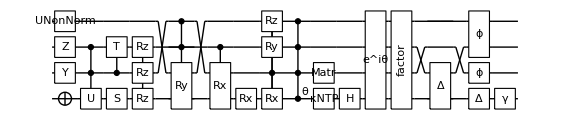

```mathematica
circ = Circuit[Subscript[Damp, 0][.1] Subscript[Deph, 1][.1] Subscript[Deph, 2,3][.5] Subscript[Depol, 0][.2] Subscript[Depol, 0,2][.4]Fac[.3+.3ⅈ]G[π] Subscript[H, 0] Subscript[Id, 1] Subscript[KrausNonTP, 0]@RandomComplex[{0,1+ⅈ},{3,2,2}]Subscript[Matr, 1]@RandomComplex[{0,1+ⅈ},{2,2}]Subscript[C, 0,1,2]@Subscript[Ph, 3][.6]Subscript[C, 1]@R[π,Subscript[X, 0] Subscript[Y, 2] Subscript[Z, 3]]Subscript[Rx, 0][.1]Subscript[C, 2]@Subscript[Rx, 1,0][.8]Subscript[C, 1,2]@Subscript[Ry, 3,0][π/3]Subscript[Rz, 0,1,2][.9] Subscript[S, 0] Subscript[C, 1][Subscript[T, 2]]Subscript[C, 1,2]@Subscript[U, 0]@RandomVariate @ CircularUnitaryMatrixDistribution[2] Subscript[UNonNorm, 3]@RandomComplex[{0,1+ⅈ},{2,2}] Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2]] // Reverse;
DrawCircuit[%]
```

```mathematica
test @ circ
```

output:   {Z_2,Z_6,Y_1,U_5[{{0,ⅈ},{-ⅈ,0}}],X_0,X_4,UNonNorm_3[{{0.939064+0.652941 ⅈ,0.714666+0.48563 ⅈ},{0.930006+0.660488 ⅈ,0.630213+0.453642 ⅈ}}],UNonNorm_7[{{0.939064-0.652941 ⅈ,0.714666-0.48563 ⅈ},{0.930006-0.660488 ⅈ,0.630213-0.453642 ⅈ}}],C_(1,2)[U_0[{{0.238006+0.0751351 ⅈ,0.43714-0.86407 ⅈ},{-0.59793+0.7617 ⅈ,-0.168787-0.183856 ⅈ}}]],C_(5,6)[U_4[{{0.238006-0.0751351 ⅈ,0.43714+0.86407 ⅈ},{-0.59793-0.7617 ⅈ,-0.168787+0.183856 ⅈ}}]],C_1[T_2],C_5[Ph_6[-π/4]],S_0,Ph_4[-π/2],Rz_(0,1,2)[0.9],Rz_(4,5,6)[-0.9],C_(1,2)[Ry_(3,0)[π/3]],C_(5,6)[Ry_(7,4)[-π/3]],C_2[Rx_(1,0)[0.8]],C_6[Rx_(5,4)[-0.8]],Rx_0[0.1],Rx_4[-0.1],C_1[R[π,X_0 Y_2 Z_3]],C_5[R[π,X_4 Y_6 Z_7]],C_(0,1,2)[Ph_3[0.6]],C_(4,5,6)[Ph_7[-0.6]],Matr_1[{{0.0433638+0.037496 ⅈ,0.747555+0.350197 ⅈ},{0.256458+0.556372 ⅈ,0.314154+0.529126 ⅈ}}],Matr_(0,4)[{{1.39652+0. ⅈ,1.14074-0.943531 ⅈ,1.14074+0.943531 ⅈ,2.47912+0. ⅈ},{1.10516+0.638879 ⅈ,1.61705-0.978374 ⅈ,0.600817+1.5064 ⅈ,2.66221+0.752945 ⅈ},{1.10516-0.638879 ⅈ,0.600817-1.5064 ⅈ,1.61705+0.978374 ⅈ,2.66221-0.752945 ⅈ},{1.45759+0. ⅈ,1.0415-1.36484 ⅈ,1.0415+1.36484 ⅈ,3.62453+0. ⅈ}}],Id_1,Id_5,H_0,H_4,Fac[0.3+0.3 ⅈ],Matr_(0,2,4,6)[{{0.68+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ},{0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.68+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.68+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.573333+0. ⅈ,0.+0. ⅈ},{0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.106667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.68+0. ⅈ}}],Matr_(0,4)[{{0.866667+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.133333+0. ⅈ},{0.+0. ⅈ,0.733333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.733333+0. ⅈ,0.+0. ⅈ},{0.133333+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.866667+0. ⅈ}}],Matr_(2,3,6,7)[{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.333333,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.333333,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}}],Matr_(1,5)[{{1.,0.,0.,0.},{0.,0.8,0.,0.},{0.,0.,0.8,0.},{0.,0.,0.,1.}}],Matr_(0,4)[{{1.,0.,0.,0.1},{0.,0.948683,0.,0.},{0.,0.,0.948683,0.},{0.,0.,0.,0.9}}]}

error:   0

## AssertValidChannels -> False

```mathematica
Fac[x];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{Fac[x]}

{Fac[x]}

```mathematica
GetCircuitSuperoperator[ G[x] ]
GetCircuitSuperoperator[ G[x], AssertValidChannels->False ]
```

{}

{G[2 ⅈ Im[x]]}

```mathematica
Subscript[Ph, 0][x];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{Ph_0[x],Ph_1[-x]}

{Ph_0[x],Ph_1[-Conjugate[x]]}

```mathematica
Subscript[C, 0,1] @ R[x,Subscript[X, 2] Subscript[Y, 3] Subscript[Z, 4]];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{C_(0,1)[R[x,X_2 Y_3 Z_4]],C_(5,6)[R[x,X_7 Y_8 Z_9]]}

{C_(0,1)[R[x,X_2 Y_3 Z_4]],C_(5,6)[R[Conjugate[x],X_7 Y_8 Z_9]]}

```mathematica
Circuit[Subscript[Rx, 0][x]Subscript[Ry, 1][y]Subscript[Rz, 2][z]];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{Rx_0[x],Rx_3[-x],Ry_1[y],Ry_4[y],Rz_2[z],Rz_5[-z]}

{Rx_0[x],Rx_3[-Conjugate[x]],Ry_1[y],Ry_4[Conjugate[y]],Rz_2[z],Rz_5[-Conjugate[z]]}

```mathematica
Circuit[Subscript[Ry, 0][x]Subscript[Ry, 0,1][x]Subscript[Ry, 0,1,2][x]Subscript[Ry, 0,1,2,3][x]];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{Ry_0[x],Ry_4[x],Ry_(0,1)[x],Ry_(4,5)[-x],Ry_(0,1,2)[x],Ry_(4,5,6)[x],Ry_(0,1,2,3)[x],Ry_(4,5,6,7)[-x]}

{Ry_0[x],Ry_4[Conjugate[x]],Ry_(0,1)[x],Ry_(4,5)[-Conjugate[x]],Ry_(0,1,2)[x],Ry_(4,5,6)[Conjugate[x]],Ry_(0,1,2,3)[x],Ry_(4,5,6,7)[-Conjugate[x]]}

```mathematica
Subscript[Damp, 0][x];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{Matr_(0,1)[{{1,0,0,x},{0,√(1-x),0,0},{0,0,√(1-x),0},{0,0,0,1-x}}]}

{Matr_(0,1)[{{1,0,0,√x Conjugate[√x]},{0,√(1-x),0,0},{0,0,Conjugate[√(1-x)],0},{0,0,0,√(1-x) Conjugate[√(1-x)]}}]}

```mathematica
Subscript[Deph, 1][x];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{Matr_(1,3)[{{1,0,0,0},{0,1-2 x,0,0},{0,0,1-2 x,0},{0,0,0,1}}]}

{Matr_(1,3)[{{√(1-x) Conjugate[√(1-x)]+√x Conjugate[√x],0,0,0},{0,√(1-x) Conjugate[√(1-x)]-√x Conjugate[√x],0,0},{0,0,√(1-x) Conjugate[√(1-x)]-√x Conjugate[√x],0},{0,0,0,√(1-x) Conjugate[√(1-x)]+√x Conjugate[√x]}}]}

```mathematica
Subscript[Deph, 0,1][x];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{Matr_(0,1,2,3)[{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1-(4 x)/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1-(4 x)/3,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1-(4 x)/3,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1-(4 x)/3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1-(4 x)/3,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1-(4 x)/3,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1-(4 x)/3,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1-(4 x)/3,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1-(4 x)/3,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1-(4 x)/3,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1-(4 x)/3,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1-(4 x)/3,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}]}

{Matr_(0,1,2,3)[{{√(1-x) Conjugate[√(1-x)]+√x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,√(1-x) Conjugate[√(1-x)]+√x Conjugate[√x],0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]+√x Conjugate[√x],0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x],0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]+√x Conjugate[√x]}}]}

```mathematica
Subscript[Depol, 0,2][x];
GetCircuitSuperoperator[%]
GetCircuitSuperoperator[%%, AssertValidChannels->False ]
```

{Matr_(0,2,3,5)[{{1-(4 x)/5,0,0,0,0,(4 x)/15,0,0,0,0,(4 x)/15,0,0,0,0,(4 x)/15},{0,1-(16 x)/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1-(16 x)/15,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1-(16 x)/15,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1-(16 x)/15,0,0,0,0,0,0,0,0,0,0,0},{(4 x)/15,0,0,0,0,1-(4 x)/5,0,0,0,0,(4 x)/15,0,0,0,0,(4 x)/15},{0,0,0,0,0,0,1-(16 x)/15,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1-(16 x)/15,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1-(16 x)/15,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1-(16 x)/15,0,0,0,0,0,0},{(4 x)/15,0,0,0,0,(4 x)/15,0,0,0,0,1-(4 x)/5,0,0,0,0,(4 x)/15},{0,0,0,0,0,0,0,0,0,0,0,1-(16 x)/15,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1-(16 x)/15,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1-(16 x)/15,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1-(16 x)/15,0},{(4 x)/15,0,0,0,0,(4 x)/15,0,0,0,0,(4 x)/15,0,0,0,0,1-(4 x)/5}}]}

{Matr_(0,2,3,5)[{{√(1-x) Conjugate[√(1-x)]+1/5 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x]},{0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0,0,0,0,0,0,0,0},{4/15 √x Conjugate[√x],0,0,0,0,√(1-x) Conjugate[√(1-x)]+1/5 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x]},{0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0,0,0},{4/15 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x],0,0,0,0,√(1-x) Conjugate[√(1-x)]+1/5 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x]},{0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,√(1-x) Conjugate[√(1-x)]-1/15 √x Conjugate[√x],0},{4/15 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x],0,0,0,0,4/15 √x Conjugate[√x],0,0,0,0,√(1-x) Conjugate[√(1-x)]+1/5 √x Conjugate[√x]}}]}

## Errors

```mathematica
GetCircuitSuperoperator[e]
```

GetCircuitSuperoperator::error: Invalid arguments. See ?GetCircuitSuperoperator

$Failed

```mathematica
GetCircuitSuperoperator[Subscript[Eh, 0,1]]
```

GetCircuitSuperoperator::error: Cannot obtain conjugate of unrecognised or unsupported operator: Eh_(0,1)

$Failed

```mathematica
GetCircuitSuperoperator @ Subscript[M, 0]
```

GetCircuitSuperoperator::error: Cannot obtain conjugate of unrecognised or unsupported operator: M_0

$Failed

```mathematica
GetCircuitSuperoperator[ Subscript[Damp, 0][-1] ]
```

GetCircuitSuperoperator::error: One or more channels could not be asserted as completely positive and trace-preserving (CPTP) and ergo could not be simplified. Prevent this error with AssertValidChannels -> False.

$Failed

```mathematica
GetCircuitSuperoperator[Subscript[Deph, 0,1][ⅈ]]
```

GetCircuitSuperoperator::error: One or more channels could not be asserted as completely positive and trace-preserving (CPTP) and ergo could not be simplified. Prevent this error with AssertValidChannels -> False.

$Failed